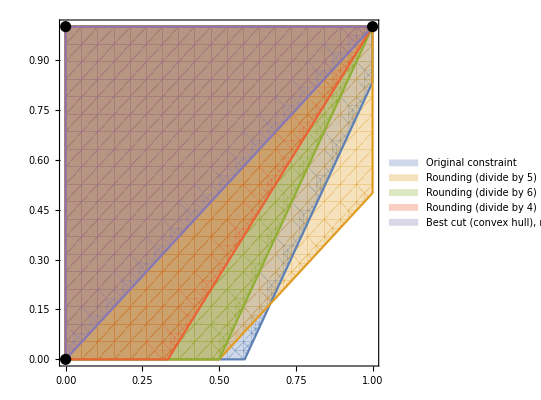

F:\Univ\_PhD\TA\MATH0462\Syllabus\5_valid_ineq_12x6y7.png

```mathematica
(* 1a. Inequalities sorted graphically (first those having the largest area). *)
p1a=RegionPlot[{12x-6y≤7,2x-2y≤1,2x-y≤1,3x-2y≤1,x-y≤0},{x,0,1},{y,0,1},
Epilog->{PointSize[.02],Point[{{0,0},{0,1},{1,1}}]},
PlotLegends->{"Original constraint","Rounding (divide by 5)","Rounding (divide by 6)","Rounding (divide by 4)","Best cut (convex hull), rounding (divide by 8)"}]
Export[NotebookDirectory[]<>"5_valid_ineq_12x6y7.png",p1a]
```

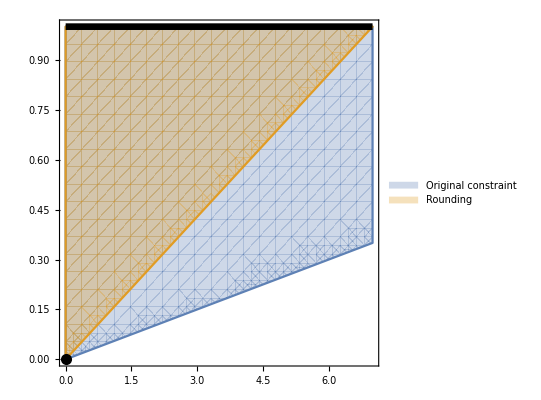

F:\Univ\_PhD\TA\MATH0462\Syllabus\5_valid_ineq_x20yx7.png

```mathematica
(* 1b. *)
p1b=RegionPlot[{x≤20y&&x≤7,x≤7y},{x,0,7},{y,0,1},
Epilog->{Thickness[.012],Line[{{0,1},{7,1}}],PointSize[.02],Point[{0,0}]},
PlotLegends->{"Original constraint","Rounding"}]
Export[NotebookDirectory[]<>"5_valid_ineq_x20yx7.png",p1b]
```

{{x→6,y→1}}

{{x→12,y→2}}

{{x→18,y→3}}

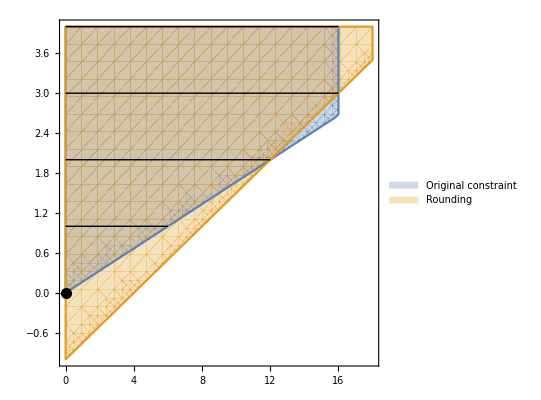

F:\Univ\_PhD\TA\MATH0462\Syllabus\5_valid_ineq_x6yx16.png

```mathematica
(* 1c. *)
Solve[x==6y&&y==1,{x,y}]
Solve[x==6y&&y==2,{x,y}]
Solve[x==6y&&y==3,{x,y}]
p1c=RegionPlot[{x≤6y&&x≤16,x≤4+4y},{x,0,18},{y,-1,4},
Epilog->{Thick,PointSize[.02],
Line[{{{0,1},{6,1}},{{0,2},{12,2}},{{0,3},{16,3}},{{0,4},{16,4}}}],
Point[{0,0}]},
PlotLegends->{"Original constraint","Rounding"}]
Export[NotebookDirectory[]<>"5_valid_ineq_x6yx16.png",p1c]
```